```mathematica
(*n = 6*)
f[x_]=√3*ⅇ^(-1/22 x^3+1/2 x-1/4);
```

```mathematica
a= 0;
b=6;
n=6;
```

```mathematica
Tablel= Table[{i ,Round[f[(a+b)/n*i],10^-4]//N},{i,0,n}];
TableForm[Tablel]
```

0 | 1.3489
1 | 2.1252
2 | 2.5489
3 | 1.7719
4 | 0.5435
5 | 0.056
6 | 0.0015

```mathematica
Fac[x_] =∏_(i=0)^n (x-(a+b)/n*i);
DifFac[x_] = D[Fac[x],x];
PolLagr[x_] = ∑_(i=0)^n f[(a+b)/n*i]*Fac[x]/((x-(a+b)/n*i)*DifFac[(a+b)/n*i]) //N;
Expand[PolLagr[x]]
```

1.34892+0.170641 x+1.16154 x^2-0.631411 x^3+0.0697816 x^4+0.00679391 x^5-0.00109457 x^6

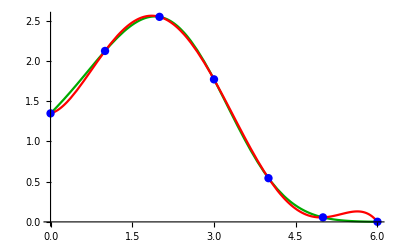

```mathematica
Show[Plot[f[x],{x,a,b}, PlotStyle->Darker[Green]],Plot[PolLagr[x],{x,a,b},PlotStyle->Red], ListPlot[Tablel,PlotStyle->{Blue,PointSize[0.015]}]]
```

```mathematica
Array[dif,{n+1},{n+1},{0,0}];
For[k=1,k≤ n,k++,
	For[i=n,i≥ n-k,i--,dif[i,k]=""]];
For[i=0,i≤n,i++,
dif[i,0]=Tablel[[i+1,2]]];
For[k=1,k≤n,k++,
	For[i=0,i≤n-k,i++,
         dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
newTablel=Array[dif,{n+1,n+1},{0,0}];
TableForm[Map[NumberForm[#,{6,3}]&,newTablel,{2}]]
```

1.349 | 0.776 | -0.353 | -0.848 | 1.597 | -1.154 | -0.789
2.125 | 0.424 | -1.201 | 0.749 | 0.443 | -1.943 | 
2.549 | -0.777 | -0.451 | 1.192 | -1.500 |  | 
1.772 | -1.228 | 0.741 | -0.308 |  |  | 
0.544 | -0.488 | 0.433 |  |  |  | 
0.056 | -0.055 |  |  |  |  | 
0.002 |  |  |  |  |  |

```mathematica
h=(b-a)/n;
q=(x-b)/h;
newFunc[x_]=dif[n,0];
P[q_]=1;
For[k=1,k≤n,k++,
P[q_]=P[q]*(q+k-1);
newFunc[x_]=newFunc[x]+dif[n-k,k]/k!*P[q]];
newFunc[x_]=Simplify[newFunc[x]]
```

1.3489+0.171137 x+1.16071 x^2-0.6309 x^3+0.0696361 x^4+0.00681333 x^5-0.00109556 x^6

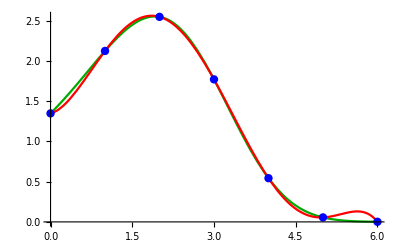

```mathematica
Show[Plot[f[x],{x,0,6}, PlotStyle->Darker[Green]],Plot[newFunc[x],{x,a,b},PlotStyle->Red], ListPlot[Tablel,PlotStyle->{ Blue,PointSize[0.015]}]]
```

```mathematica
NP[x_]=InterpolatingPolynomial[Tablel,x];
NP[x_]=Simplify[NP[x]]
```

1.3489+0.171137 x+1.16071 x^2-0.6309 x^3+0.0696361 x^4+0.00681333 x^5-0.00109556 x^6

```mathematica
Show[Plot[f[x],{x,0,6}, PlotStyle->Darker[Green]],Plot[NP[x],{x,a,b},PlotStyle->Red], ListPlot[Tablel,PlotStyle->{ Blue,PointSize[0.015]}]]
```

-Graphics-

```mathematica
Grid[{{"f[2.4316] =",Row[{f[2.4316]//N,"  (",FullForm[f[2.4316]],")"}]},{"L[2.4316] =",Row[{PolLagr[2.4316]//N,"  (",FullForm[PolLagr[2.4316]],")"}]},{"P[2.4316] =",Row[{newFunc[2.4316]//N,"  (",FullForm[newFunc[2.4316]],")"}]},{"NP[2.4316] =",Row[{NP[2.4316]//N,"  (",FullForm[NP[2.4316]],")"}]}}]
```

f[2.4316] = | 2.36693  (2.36693)
L[2.4316] = | 2.34451  (2.34451)
P[2.4316] = | 2.34451  (2.34451)
NP[2.4316] = | 2.34451  (2.34451)

```mathematica
Delta[x_]=Abs[f[x]-NP[x]];
```

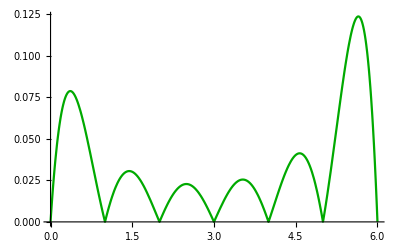

```mathematica
Plot[Delta[x],{x,a,b}, PlotStyle->Darker[Green]]
```

```mathematica
FindMaximum[Delta[x],{x,5,6}]
```

{0.123798,{x→5.64944}}

```mathematica
(*n = 10*)
```

```mathematica
a= 0;
b=6;
n=10;
```

```mathematica
Tablel= Table[{(b-a)/n*i,Round[f[(a+b)/n*i],10^-4]//N},{i,0,n}] // N;
```

```mathematica
TableForm[Tablel]
```

0. | 1.3489
0.6 | 1.8031
1.2 | 2.2722
1.8 | 2.5452
2.4 | 2.3892
3. | 1.7719
3.6 | 0.9788
4.2 | 0.3797
4.8 | 0.0975
5.4 | 0.0156
6. | 0.0015

```mathematica
Fac[x_] =∏_(i=0)^n (x-(a+b)/n*i);
DifFac[x_] = D[Fac[x],x];
PolLagr[x_] = ∑_(i=0)^n f[(a+b)/n*i]*Fac[x]/((x-(a+b)/n*i)*DifFac[(a+b)/n*i]) //N;
Expand[PolLagr[x]]
```

1.34892+0.59014 x+0.533464 x^2-0.638119 x^3+0.469139 x^4-0.212124 x^5+0.0289678 x^6+0.00865659 x^7-0.00349156 x^8+0.000438572 x^9-0.000019431 x^10

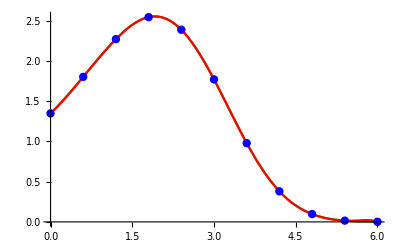

```mathematica
Show[Plot[f[x],{x,a,b}, PlotStyle->Darker[Green]],Plot[PolLagr[x],{x,a,b},PlotStyle->Red], ListPlot[Tablel,PlotStyle->{Blue,PointSize[0.015]}]]
```

```mathematica
Array[dif,{n+1},{n+1},{0,0}];
For[k=1,k≤ n,k++,
	For[i=n,i≥ n-k,i--,dif[i,k]=""]];
For[i=0,i≤n,i++,
dif[i,0]=Tablel[[i+1,2]]];
For[k=1,k≤n,k++,
	For[i=0,i≤n-k,i++,
         dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
newTablel=Array[dif,{n+1,n+1},{0,0}];
TableForm[Map[NumberForm[#,{6,3}]&,newTablel,{2}]]
```

1.349 | 0.454 | 0.015 | -0.211 | -0.022 | 0.222 | -0.105 | -0.245 | 0.498 | -0.315 | -0.427
1.803 | 0.469 | -0.196 | -0.233 | 0.201 | 0.117 | -0.351 | 0.253 | 0.183 | -0.742 | 
2.272 | 0.273 | -0.429 | -0.032 | 0.318 | -0.234 | -0.098 | 0.436 | -0.559 |  | 
2.545 | -0.156 | -0.461 | 0.286 | 0.084 | -0.331 | 0.339 | -0.122 |  |  | 
2.389 | -0.617 | -0.176 | 0.370 | -0.247 | 0.007 | 0.216 |  |  |  | 
1.772 | -0.793 | 0.194 | 0.123 | -0.239 | 0.224 |  |  |  |  | 
0.979 | -0.599 | 0.317 | -0.117 | -0.016 |  |  |  |  |  | 
0.380 | -0.282 | 0.200 | -0.133 |  |  |  |  |  |  | 
0.098 | -0.082 | 0.068 |  |  |  |  |  |  |  | 
0.016 | -0.014 |  |  |  |  |  |  |  |  | 
0.002 |  |  |  |  |  |  |  |  |  |

```mathematica
h=(b-a)/n;
q=(x-b)/h;
newFunc[x_]=dif[n,0];
P[q_]=1;
For[k=1,k≤n,k++,
P[q_]=P[q]*(q+k-1);
newFunc[x_]=newFunc[x]+dif[n-k,k]/k!*P[q]];
newFunc[x_]=Simplify[newFunc[x]]
```

1.3489+0.590439 x+0.533176 x^2-0.638429 x^3+0.469629 x^4-0.212318 x^5+0.0289717 x^6+0.00867371 x^7-0.00349649 x^8+0.000439145 x^9-0.0000194559 x^10

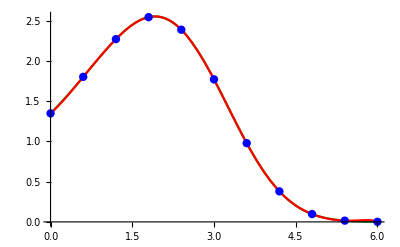

```mathematica
Show[Plot[f[x],{x,0,6}, PlotStyle->Darker[Green]],Plot[newFunc[x],{x,a,b},PlotStyle->Red], ListPlot[Tablel,PlotStyle->{ Blue,PointSize[0.015]}]]
```

```mathematica
NP[x_]=InterpolatingPolynomial[Tablel,x];
NP[x_]=Simplify[NP[x]]
```

1.3489+0.590439 x+0.533176 x^2-0.638429 x^3+0.469629 x^4-0.212318 x^5+0.0289717 x^6+0.00867371 x^7-0.00349649 x^8+0.000439145 x^9-0.0000194559 x^10

```mathematica
Show[Plot[f[x],{x,0,6}, PlotStyle->Darker[Green]],Plot[NP[x],{x,a,b},PlotStyle->Red], ListPlot[Tablel,PlotStyle->{ Blue,PointSize[0.015]}]]
```

-Graphics-

```mathematica
Grid[{{"f[2.4316] =",Row[{f[2.4316]//N,"  (",FullForm[f[2.4316]],")"}]},{"L[2.4316] =",Row[{PolLagr[2.4316]//N,"  (",FullForm[PolLagr[2.4316]],")"}]},{"P[2.4316] =",Row[{newFunc[2.4316]//N,"  (",FullForm[newFunc[2.4316]],")"}]},{"NP[2.4316] =",Row[{NP[2.4316]//N,"  (",FullForm[NP[2.4316]],")"}]}}]
```

f[2.4316] = | 2.36693  (2.36693)
L[2.4316] = | 2.36689  (2.36689)
P[2.4316] = | 2.36693  (2.36693)
NP[2.4316] = | 2.36693  (2.36693)

```mathematica
Delta[x_]=Abs[f[x]-NP[x]];
```

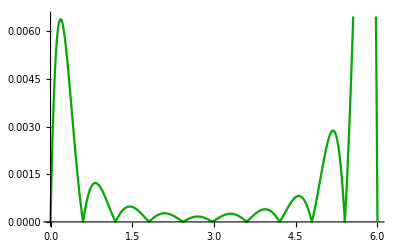

```mathematica
Plot[Delta[x],{x,a,b}, PlotStyle->Darker[Green]]
```

```mathematica
FindMaximum[Delta[x],{x,5.5,6}]
```

{0.0185966,{x→5.82391}}

```mathematica
(*2 Номер*)
```

```mathematica
(*n = 6*)
a= 0;
b=6;
n=6;

ChebConst =Table[Cos[Pi*(2*i+1)/(2*n+2)],{i,0,n}];
Table2=Table[{Round[(a+b)/2+(b-a)/2*ChebConst[[n-i+1]], 10^-3]//N,Round[f[(a+b)/2+(b-a)/2*ChebConst[[n-i+1]]], 10^-3]//N},{i,0,n}];
TableForm[Table2]
```

0.075 | 1.401
0.655 | 1.847
1.698 | 2.524
3. | 1.772
4.302 | 0.311
5.345 | 0.019
5.925 | 0.002

```mathematica
Array[dif,{n+1},{n+1},{0,0}];
For[i=1,i≤ n,i++,
	For[j=n,j≥ n-i,j--,dif[j,i]=""]];
For[i=0,i≤n,i++,dif[i,0]=Table2[[i+1,2]]];
For[i=1,i≤n,i++,
	For[j=0,j≤n-i,j++,
         dif[j,i]=(dif[j+1,i-1]-dif[j,i-1])/(Table2[[j+i+1,1]]-Table2[[j+1,1]])]];

newTable=Array[dif,{n+1,n+1},{0,0}];
TableForm[Map[NumberForm[#,{6,3}]&,newTable,{2}]]
```

1.401 | 0.769 | -0.074 | -0.154 | 0.057 | -0.008 | -0.001
1.847 | 0.649 | -0.523 | 0.086 | 0.015 | -0.013 | 
2.524 | -0.578 | -0.209 | 0.156 | -0.053 |  | 
1.772 | -1.122 | 0.359 | -0.070 |  |  | 
0.311 | -0.280 | 0.154 |  |  |  | 
0.019 | -0.029 |  |  |  |  | 
0.002 |  |  |  |  |  |

```mathematica
newFunc[x_]=dif[0,0];
P[x_]=1;
For[k=1,k≤n,k++,
P[x_]=P[x]*(x-Table2[[k,1]]);
newFunc[x_]=newFunc[x]+dif[0,k]*P[x]];
newFunc[x_]=Simplify[newFunc[x]]
```

1.37031+0.344139 x+0.907246 x^2-0.533384 x^3+0.0619427 x^4+0.00499361 x^5-0.000857848 x^6

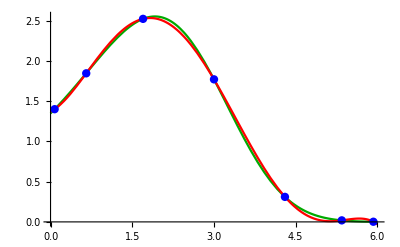

```mathematica
Show[Plot[f[x],{x,a,b}, PlotStyle->Darker[Green]],Plot[newFunc[x],{x,a,b},PlotStyle->Red], ListPlot[Table2,PlotStyle->{ Blue,PointSize[0.015]}]]
```

```mathematica
NP=Interpolation[Table2];
```

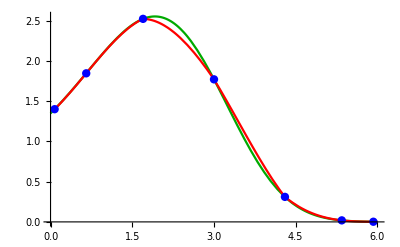

```mathematica
Show[Plot[f[x],{x,a,b}, PlotStyle->Darker[Green]],Plot[NP[x],{x,a+0.1,b},PlotStyle->Red], ListPlot[Table2,PlotStyle->{ Blue,PointSize[0.015]}]]
```

```mathematica
Grid[{{"f[2.4316] =",Row[{f[2.4316]//N,"  (",FullForm[f[2.4316]],")"}]},{"Pnr[2.4316] =",Row[{newFunc[2.4316]//N,"  (",FullForm[newFunc[2.4316]],")"}]},{"Intf[2.4316] =",Row[{NP[2.4316]//N,"  (",FullForm[NP[2.4316]],")"}]}}]
```

f[2.4316] = | 2.36693  (2.36693)
Pnr[2.4316] = | 2.31544  (2.31544)
Intf[2.4316] = | 2.25464  (2.25464)

```mathematica
Delta[x_]=Abs[f[x]-newFunc[x]];
```

```mathematica
FindMaximum[Delta[x],{x,1,6}]
```

{0.034153,{x→1.1818}}

```mathematica
Delta[x_]=Abs[f[x]-NP[x]];
FindMaximum[Delta[x],{x,1,6}]
```

{0.114273,{x→2.35311}}

```mathematica
(*n = 10*)
```

```mathematica
a= 0;
b=6;
n=10;
```

```mathematica
ChebConst =Table[Cos[Pi*(2*i+1)/(2*n+2)],{i,0,n}];
Table2=Table[{Round[(a+b)/2+(b-a)/2*ChebConst[[n-i+1]], 10^-3]//N,Round[f[(a+b)/2+(b-a)/2*ChebConst[[n-i+1]]], 10^-3]//N},{i,0,n}];
TableForm[Table2]
```

0.031 | 1.37
0.271 | 1.543
0.733 | 1.911
1.378 | 2.385
2.155 | 2.514
3. | 1.772
3.845 | 0.696
4.622 | 0.153
5.267 | 0.024
5.729 | 0.005
5.969 | 0.002

```mathematica
Array[dif,{n+1},{n+1},{0,0}];
For[i=1,i≤ n,i++,
	For[j=n,j≥ n-i,j--,dif[j,i]=""]];
For[i=0,i≤n,i++,dif[i,0]=Table2[[i+1,2]]];
For[i=1,i≤n,i++,
	For[j=0,j≤n-i,j++,
         dif[j,i]=(dif[j+1,i-1]-dif[j,i-1])/(Table2[[j+i+1,1]]-Table2[[j+1,1]])]];

newTable=Array[dif,{n+1,n+1},{0,0}];
TableForm[Map[NumberForm[#,{6,5}]&,newTable,{2}]]
```

1.37000 | 0.72083 | 0.10784 | -0.12141 | -0.02889 | 0.01902 | -0.00056 | -0.00157 | 0.00052 | -0.00006 | -0.00001
1.54300 | 0.79654 | -0.05569 | -0.18278 | 0.02759 | 0.01688 | -0.00776 | 0.00117 | 0.00016 | -0.00014 | 
1.91100 | 0.73488 | -0.40004 | -0.10749 | 0.08793 | -0.01688 | -0.00191 | 0.00204 | -0.00064 |  | 
2.38500 | 0.16602 | -0.64373 | 0.16613 | 0.02227 | -0.02555 | 0.00827 | -0.00133 |  |  | 
2.51400 | -0.87811 | -0.23389 | 0.23839 | -0.07709 | 0.01044 | 0.00218 |  |  |  | 
1.77200 | -1.27337 | 0.35421 | -0.00150 | -0.03977 | 0.01875 |  |  |  |  | 
0.69600 | -0.69884 | 0.35080 | -0.11002 | 0.01589 |  |  |  |  |  | 
0.15300 | -0.20000 | 0.14352 | -0.07627 |  |  |  |  |  |  | 
0.02400 | -0.04113 | 0.04078 |  |  |  |  |  |  |  | 
0.00500 | -0.01250 |  |  |  |  |  |  |  |  | 
0.00200 |  |  |  |  |  |  |  |  |  |

```mathematica
newFunc[x_]=dif[0,0];
P[x_]=1;
For[k=1,k≤n,k++,
P[x_]=P[x]*(x-Table2[[k,1]]);
newFunc[x_]=newFunc[x]+dif[0,k]*P[x]];
newFunc[x_]=Simplify[newFunc[x]]
```

1.34947+0.653446 x+0.291348 x^2-0.309422 x^3+0.26391 x^4-0.15804 x^5+0.0317289 x^6+0.00324037 x^7-0.00211203 x^8+0.000285795 x^9-0.0000129367 x^10

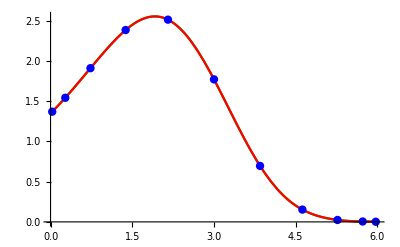

```mathematica
Show[Plot[f[x],{x,a,b}, PlotStyle->Darker[Green]],Plot[newFunc[x],{x,a,b},PlotStyle->Red], ListPlot[Table2,PlotStyle->{ Blue,PointSize[0.015]}]]
```

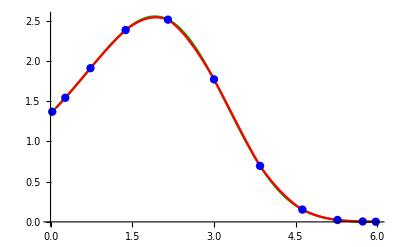

```mathematica
NP=Interpolation[Table2];
Show[Plot[f[x],{x,a,b}, PlotStyle->Darker[Green]],Plot[NP[x],{x,a+0.1,b},PlotStyle->Red], ListPlot[Table2,PlotStyle->{ Blue,PointSize[0.015]}]]
```

```mathematica
Grid[{{"f[2.4316] =",Row[{f[2.4316]//N,"  (",FullForm[f[2.4316]],")"}]},{"Pnr[2.4316] =",Row[{newFunc[2.4316]//N,"  (",FullForm[newFunc[2.4316]],")"}]},{"Intf[2.4316] =",Row[{NP[2.4316]//N,"  (",FullForm[NP[2.4316]],")"}]}}]
```

f[2.4316] = | 2.36693  (2.36693)
Pnr[2.4316] = | 2.36575  (2.36575)
Intf[2.4316] = | 2.3448  (2.3448)

```mathematica
Delta[x_]=Abs[f[x]-newFunc[x]];
FindMaximum[Delta[x],{x,1,6}]
```

{0.00134433,{x→1.04312}}

```mathematica
Delta[x_]=Abs[f[x]-NP[x]];
FindMaximum[Delta[x],{x,1,6}]
```

{0.00420316,{x→1.1438}}

```mathematica
(*N3*)
y[x_]=√3*ⅇ^(-1/22 x^3+1/2 x-1/4);
a= 0;
b=6;
n=10;
```

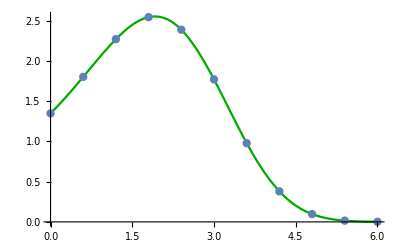

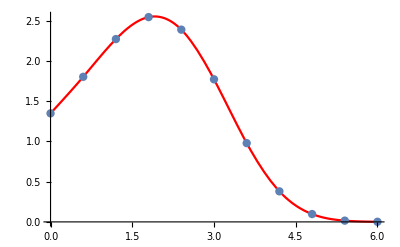

```mathematica
data={{0,1.3489},{0.6,1.8031},{1.2,2.2722},{1.8,2.5452},{2.4,2.3892},{3,1.7719},{3.6,0.9788},{4.2,0.3797},{4.8,0.0975},{5.4,0.0156},{6,0.0015}};

f[x_]:=Sqrt[3]*E^(-1/22 x^3+1/2 x-1/4);

n=Length[data];
h=Table[data[[i+1,1]]-data[[i,1]],{i,n-1}];
a=Table[data[[i,2]],{i,n}];
alpha=Table[3/h[[i]]*(a[[i+1]]-a[[i]])-3/h[[i-1]]*(a[[i]]-a[[i-1]]),{i,2,n-1}];
l=Table[0,{i,n}];
mu=Table[0,{i,n}];
z=Table[0,{i,n}];
l[[1]]=1;
mu[[1]]=0;
z[[1]]=0;
For[i=2,i<=n-1,i++,l[[i]]=2*(data[[i+1,1]]-data[[i-1,1]])-h[[i-1]]*mu[[i-1]];
mu[[i]]=h[[i]]/l[[i]];
z[[i]]=(alpha[[i-1]]-h[[i-1]]*z[[i-1]])/l[[i]];]
l[[n]]=1;
z[[n]]=0;
c=Table[0,{i,n}];
b=Table[0,{i,n-1}];
d=Table[0,{i,n-1}];
For[j=n-1,j>=1,j--,c[[j]]=z[[j]]-mu[[j]]*c[[j+1]];
b[[j]]=(a[[j+1]]-a[[j]])/h[[j]]-h[[j]]*(c[[j+1]]+2*c[[j]])/3;
d[[j]]=(c[[j+1]]-c[[j]])/(3*h[[j]]);]

S3[x_]:=Module[{j},j=1;
While[x>data[[j+1,1]],j++];
a[[j]]+b[[j]]*(x-data[[j,1]])+c[[j]]*(x-data[[j,1]])^2+d[[j]]*(x-data[[j,1]])^3]

Show[Plot[f[x],{x,0,6}, PlotStyle->Darker[Green]],ListPlot[data,PlotStyle->PointSize[0.015], PlotStyle->Blue]]
Show[Plot[S3[x],{x,0,6}, PlotStyle->Red],  ListPlot[data,PlotStyle->PointSize[0.015], PlotStyle->Blue]]
```

-Graphics-

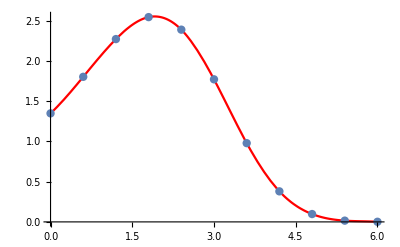

```mathematica
spl1=Interpolation[Tablel, Method->"Spline"];

gr1 = Plot[f[x], {x, 0, 6}, PlotStyle->Darker[Green]];
gr2 = ListPlot[Tablel, PlotStyle->PointSize[0.015], PlotStyle->Blue];
gr3 = Plot[spl1[x],{x, 0, 6}, PlotStyle->Red];

Show[gr1, gr2]
Show[gr3, gr2]
```

-Graphics-

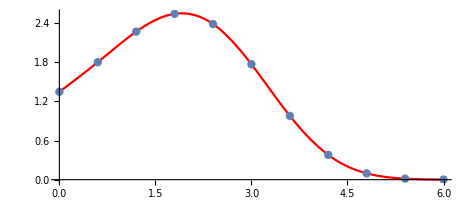

```mathematica
Needs["Splines`"]
spl2=SplineFit[Tablel, Cubic];
gr4=ParametricPlot[spl2[x],{x,0,10},PlotStyle->Red,PlotStyle->Thickness[0.0015]];
Show[gr1, gr2]
Show[gr4, gr2]
```

```mathematica
Round[f[2.4316],10^-3]//N
Round[S3[2.4316],10^-3] // N
Round[spl1[2.4316],10^-3] // N
Round[Last[spl2[2.4316/0.6]],10^-3]// N
```

2.367

2.367

2.367

«1 more identical outputs»

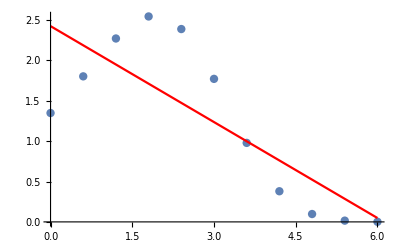

```mathematica
(*N5*)

n=Length[data];
xValues=data[[All,1]];
yValues=data[[All,2]];
sumX=Total[xValues];
sumY=Total[yValues];
sumXY=Total[xValues*yValues];
sumX2=Total[xValues^2];
a1=(n*sumXY-sumX*sumY)/(n*sumX2-sumX^2);
a0=(sumY-a1*sumX)/n;
Q1[x_]:=a0+a1*x;


Show[ListPlot[data, PlotStyle->PointSize[0.015],PlotStyle->Blue],Plot[Q1[x],{x,0,6},PlotStyle->Red]]
```

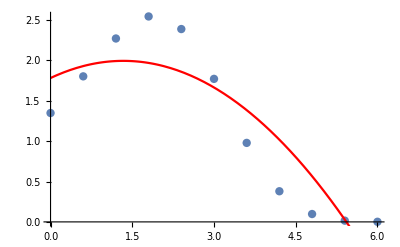

```mathematica
dataf = Table[{data[[i, 1]], f[data[[i, 1]]]}, {i, Length[data]}];


n = Length[data];
A = Table[{1, data[[i, 1]], data[[i, 1]]^2}, {i, n}];


B = Table[data[[i, 2]], {i, n}];


sol = LinearSolve[Transpose[A].A, Transpose[A].B];


Q2[x_] := sol[[1]] + sol[[2]] x + sol[[3]] x^2;

(* Строим график *)
Show[ListPlot[data, PlotStyle->PointSize[0.015],PlotStyle->Blue], Plot[Q2[x], {x, 0, 6}, PlotStyle->Red]]
```

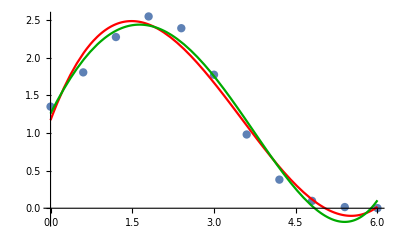

```mathematica
Q3[x_]=Fit[data,{1,x,x^2,x^3},x];
Q4[x_] = Fit[data, {1, x, x^2, x^3, x^4},x];

Show[ListPlot[data,PlotStyle->PointSize[0.015],PlotStyle->Blue],Plot[Q3[x],{x,0,6},PlotStyle->Red],Plot[Q4[x],
{x,0,6},PlotStyle->Darker[Green]],PlotRange->All]
```

```mathematica
Q1[2.4316]
Q2[2.4316]
Q3[2.4316]
Q4[2.4316]
```

1.46192

1.85214

2.12492

2.18583

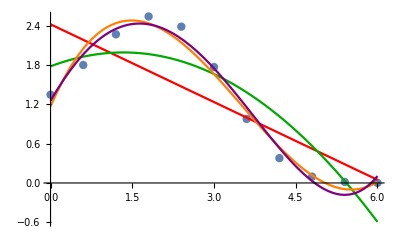

```mathematica
Show[ListPlot[data,PlotStyle->PointSize[0.015],PlotStyle->Blue],Plot[Q1[x],{x,0,6},PlotStyle->Red],Plot[Q2[x],
{x,0,6},PlotStyle->Darker[Green]],Plot[Q3[x],{x,0,6},PlotStyle->Orange], Plot[Q4[x],{x,0,6},PlotStyle->Purple],PlotRange->All]
```